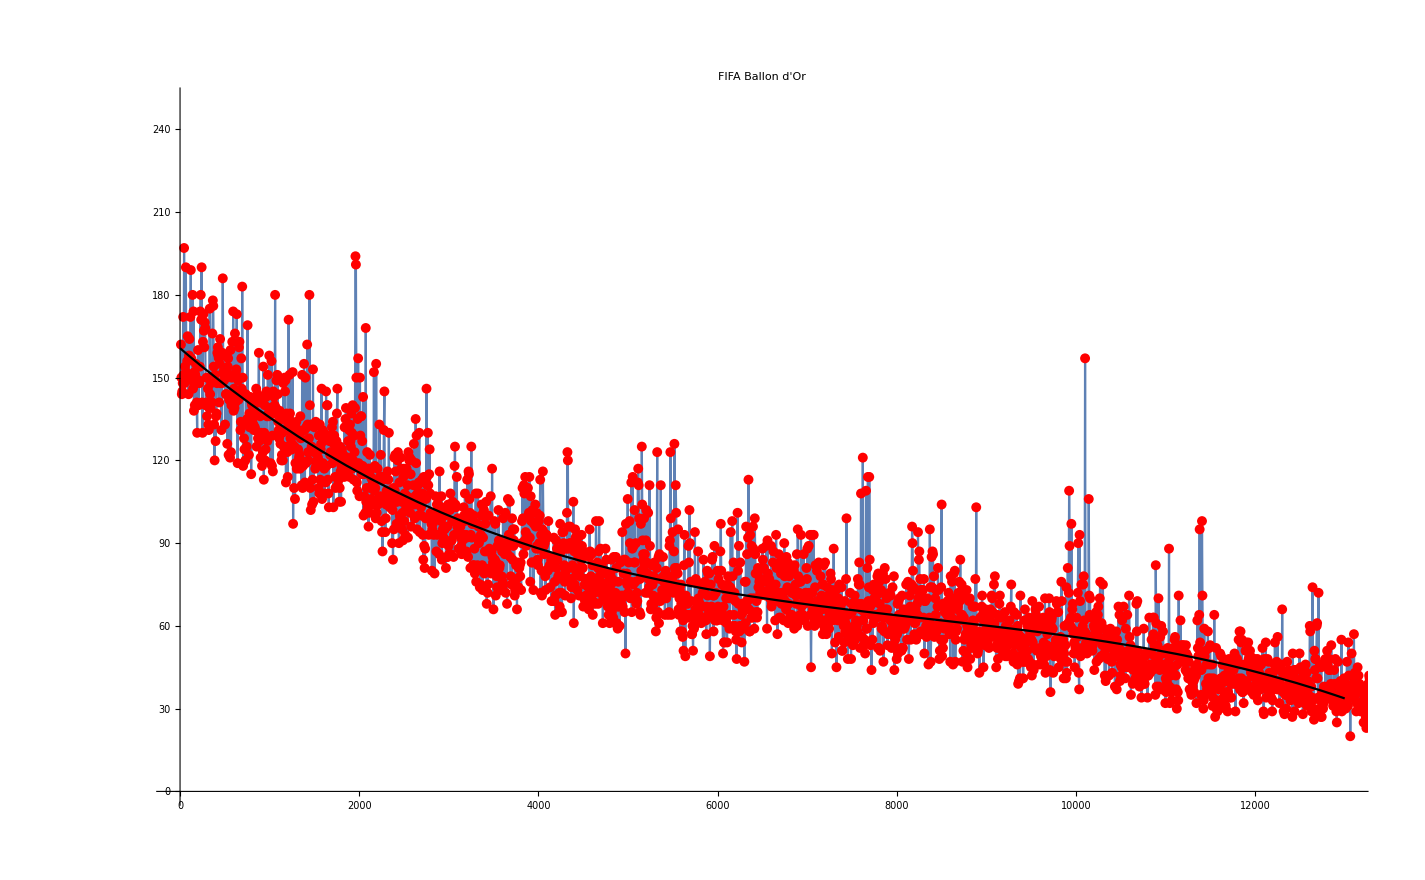

```mathematica
timestamps = Import["/home/varderes/PycharmProjects/tweet/ces_timestamps.txt","Table"];
lineplot=ListLinePlot[timestamps,PlotRange->{{0,13000},{0,250}}];
pointplot=ListPlot[timestamps,PlotStyle->Directive[Red,PointSize[0.005]],PlotRange->{{0,13000},{0,250}}];
trendline = Fit[timestamps,{1,x,x^2,x^3},x];
trendplot = Plot[trendline,{x,0,13000},PlotStyle->Black];
Show[lineplot,pointplot,trendplot,PlotLabel->Style["FIFA Ballon d'Or", FontSize->32]]
```

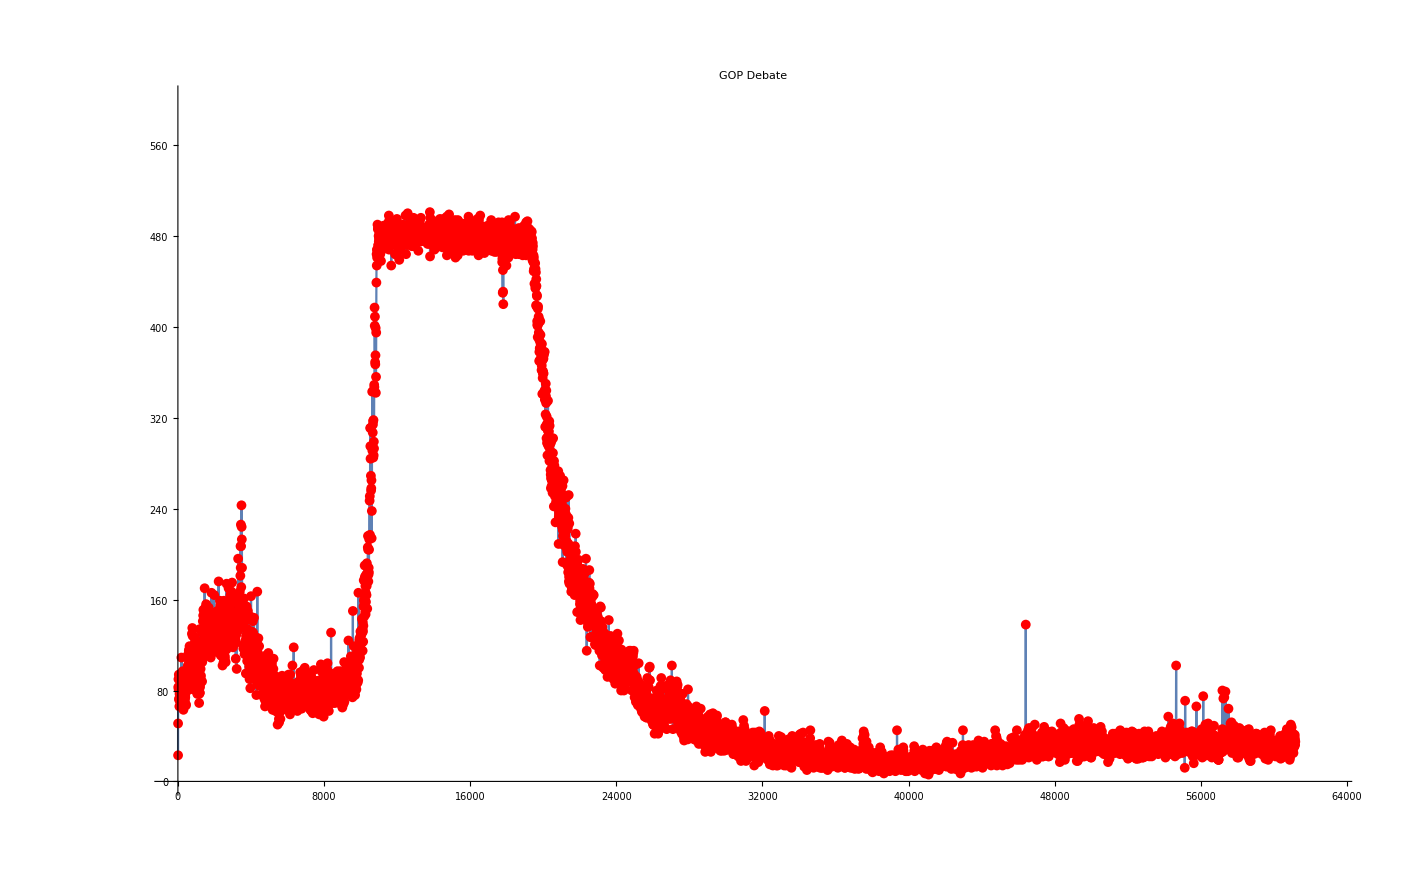

```mathematica
gop = Import["C:/Users/barse/Documents/Network Projects/tweet/gopdebate_timestamps.txt","Table"];
lineplot2=ListLinePlot[gop,PlotRange->{{0,63000},{0,600}}];
pointplot2=ListPlot[gop,PlotStyle->Directive[Red,PointSize[0.005]],PlotRange->{{0,63000},{0,600}}];
trendline2= Fit[gop,{1,x,x^2,x^3,x^4,x^5},x];
trendplot2 = Plot[trendline2,{x,0,63000},PlotStyle->Black];
Show[lineplot2,pointplot2,PlotLabel->Style["GOP Debate", FontSize->32]]
```